Definition of the vectors and matrices:

```mathematica
V={{1},{0}};
H={{0},{1}};
i_,j_:=ArrayFlatten[TensorProduct[i,j]]
y__:= y†
Z={{1,0},{0,-1}};
X={{0,1},{1,0}};
Y={{0,-I},{I,0}};
Id={{1,0},{0,1}};
```

```mathematica
WP[θ_, η_]:=Exp[-I η/2] {{Cos[θ]^2+Exp[I η] Sin[θ]^2,(1-Exp[I η]) Cos[θ]Sin[θ]},{(1-Exp[I η]) Cos[θ]Sin[θ],Sin[θ]^2+Exp[I η] Cos[θ]^2}};

WPH[θ_]:=Exp[-I π/2] {{Cos[θ]^2-Sin[θ]^2,2 Cos[θ]Sin[θ]},{2 Cos[θ]Sin[θ],Sin[θ]^2-Cos[θ]^2}};
WPQ[θ_]:=Exp[-I π/4] {{Cos[θ]^2+I Sin[θ]^2,Cos[θ]Sin[θ](1-I)},{Cos[θ]Sin[θ](1-I),Sin[θ]^2+I Cos[θ]^2}};
InitialState[α_,δ_]=√α V+Exp[I δ] √(1-α)H;
Refine[InitialState[α,δ]†,{α,δ}∈Reals && 0<α<1 && 0<δ<2π];
```

```mathematica
bell={{0,0,0,0},{0,0.5,0.5,0},{0,0.5,0.5,0},{0,0,0,0}};

θ1=0;
φ1=π/2;

θ2=0;
φ2=π/2;
KroneckerProduct[WP[φ1,π/2].WP[θ1,π],WP[φ2,π/2].WP[θ2,π]]//MatrixForm
new=KroneckerProduct[WP[φ1,π/2].WP[θ1,π],WP[φ2,π/2].WP[θ2,π]].bell.(KroneckerProduct[WP[φ1,π/2].WP[θ1,π],WP[φ2,π/2].WP[θ2,π]])†;
new//MatrixForm
base=KroneckerProduct[V,V];
prob=base†.new.base
base=KroneckerProduct[V,H];
prob=base†.new.base
base=KroneckerProduct[H,V];
prob=base†.new.base
base=KroneckerProduct[H,H];
prob=base†.new.base
```

(-ⅈ | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ)

(0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.5+0. ⅈ | 0.5+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.5+0. ⅈ | 0.5+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

{{0.+0. ⅈ}}

{{0.5+0. ⅈ}}

{{0.5+0. ⅈ}}

{{0.+0. ⅈ}}

Defining the measurement angles:

```mathematica
φ=π/2;
θ=π/4;
(WP[φ,π/2].WP[θ,π]).Z.(WP[φ,π/2].WP[θ,π])†//FullSimplify//MatrixForm
```

(-1 | 0
0 | 1)

```mathematica
φ=π/4;
θ=0;
(WP[φ,π/2,].WP[θ,π,]).(InitialState[1,0])/-(-1)^(2/4)//FullSimplify//MatrixForm
```

(1/(√2)
-ⅈ/(√2))

Probability equations for a mixed input state:

```mathematica
FinalState[θH_,θQ_,α_,δ_]=Refine[WP[θQ,π/2].WP[θH,π].InitialState[α,δ],{θH,θQ,α,δ}∈Reals && 0<α<1 && 0<θH<2π && 0<θQ<2π && 0<δ<2π ]//FullSimplify;
FinalStateC[θH_,θQ_,α_,δ_]=Refine[InitialState[α,δ]†,{α,δ}∈Reals && 0<δ<2π && 0<α<1].Refine[WP[θH,π]†, 0<θH<2π].Refine[WP[θQ,π/2]†, 0<θQ<2π]//FullSimplify;

ProjectionBasis[β_,ϕ_]=√β V+Exp[I p]√(1-β)H;
ProjectionBasisC[β_,ϕ_]=Transpose[√β V+Exp[-I ϕ]√(1-β)H];

probability[α_,δ_,θH_,θQ_,β_,ϕ_]=Refine[(ProjectionBasisC[β,ϕ].FinalState[θH,θQ,α,δ].FinalStateC[θH,θQ,α,δ].ProjectionBasis[β,ϕ]), {θH,θQ,α,δ,β,ϕ}∈Reals && 0<α<1 && 0<β<1&& 0<θH<2π && 0<θQ<2π && 0<δ<2π && 0<ϕ<2π ][[1]][[1]]//FullSimplify;
```

```mathematica
probability[α,δ,0,θQ,1,0]//FullSimplify
```

Defining the final state:

```mathematica
FinalState[θH_,θQ_,α_,δ_]=Refine[WP[θQ,π/2].WP[θH,π].InitialState[α,δ],{θH,θQ,α,δ}∈Reals && 0<α<1 && 0<θH<2π && 0<θQ<2π && 0<δ<2π ]//FullSimplify;
FinalStateC[θH_,θQ_,α_,δ_]=Refine[InitialState[α,δ]†,{α,δ}∈Reals && 0<δ<2π && 0<α<1].Refine[WP[θH,π]†, 0<θH<2π].Refine[WP[θQ,π/2]†, 0<θQ<2π]//FullSimplify;

ProjectionBasis[β_,ϕ_]=√β V+Exp[I p]√(1-β)H;
ProjectionBasisC[β_,ϕ_]=Transpose[√β V+Exp[-I ϕ]√(1-β)H];

probability[α_,δ_,θH_,θQ_,β_,ϕ_]=Refine[(ProjectionBasisC[β,ϕ].FinalState[θH,θQ,α,δ].FinalStateC[θH,θQ,α,δ].ProjectionBasis[β,ϕ]), {θH,θQ,α,δ,β,ϕ}∈Reals && 0<α<1 && 0<β<1&& 0<θH<2π && 0<θQ<2π && 0<δ<2π && 0<ϕ<2π ][[1]][[1]]//FullSimplify;
```

```mathematica
probability[0,0,θH,0,1,0]//FullSimplify
probability[α,δ,0,θQ,1,0]//FullSimplify
```

Sin[2 θH]^2

1/2 ⅇ^(-ⅈ δ) (ⅇ^(ⅈ δ) √α (-ⅈ+Cos[2 θQ])-√(1-α) Sin[2 θQ]) (√α (ⅈ+Cos[2 θQ])-ⅇ^(ⅈ δ) √(1-α) Sin[2 θQ])

Checking how we can distinguish between positive and negative rotations of the WP (We need to have the sin not centered for two different directions for the QWP and HWP):

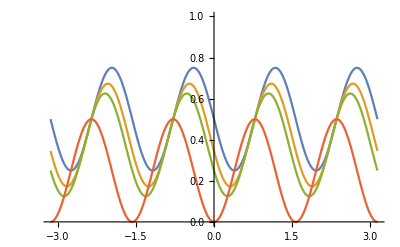

```mathematica
Plot[{probability[0,0,π/8,θQ,1,0], probability[0,0,π/10,θQ,1,0], probability[0,0,π/12,θQ,1,0],probability[0,0,0,θQ,1,0]},{θQ,-π,π}, PlotRange->{0,1}]
```

```mathematica
Plot[{probability[0,0,-π/8,-θQ,1,0], probability[0,0,-π/10,-θQ,1,0], probability[0,0,-π/12,-θQ,1,0],probability[0,0,0,-θQ,1,0]},{θQ,-π,π}, PlotRange->{0,1}]
```

-Graphics-

Checking the difference the perfect and imperfect measurements/inputs:

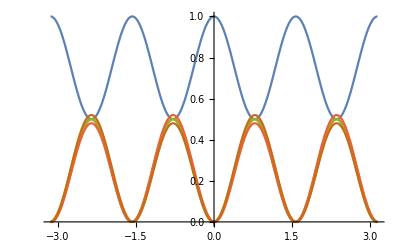

```mathematica
Plot[{probability[1,0,0,θQ,1,0], probability[0.0004,0,0,θQ,1,0], probability[0.0004,π,0,θQ,1,0], probability[0.0004,π/2,0,θQ,1,0],, probability[0.0004,-π/2,0,θQ,1,0]},{θQ,-π,π}, PlotRange->{0,1}]
```

```mathematica
FinalState[θQ_,α_,δ_]=Refine[WP[θQ,π/2].InitialState[α,δ],{θQ,α,δ}∈Reals && 0<α<1  && 0<θQ<2π && 0<δ<2π ]//FullSimplify;
FinalStateC[θQ_,α_,δ_]=Refine[InitialState[α,δ]†,{α,δ}∈Reals && 0<δ<2π && 0<α<1].Refine[WP[θQ,π/2]†, 0<θQ<2π]//FullSimplify;


ProjectionBasis[β_,ϕ_]=√β V+Exp[I ϕ] √(1-β)H;
ProjectionBasisC[β_,ϕ_]=Transpose[√β V+Exp[-I ϕ] √(1-β)H];

probability[α_,δ_,θQ_,β_,ϕ_]=Refine[(ProjectionBasisC[β,ϕ].FinalState[θH,θQ,α,δ,0,0].FinalStateC[θH,θQ,α,δ].ProjectionBasis[β,ϕ]), {θH,θQ,α,δ,β,ϕ}∈Reals && 0<α<1 && 0<β<1&& 0<θH<2π && 0<θQ<2π && 0<δ<2π && 0<ϕ<2π ][[1]][[1]]//FullSimplify
```

This shows that the wrong QWP angle can also propagate an error to the HWP (but it should also be visible because the amplitude decreases):

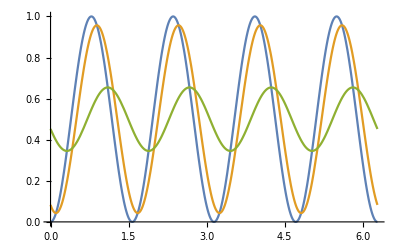

```mathematica
Plot[{probability[1,0,θH,0,0, 0,0,0],probability[1,0,θH,π/15,0, 0,0,0],probability[1,0,θH,π/5,0, 0,0,0]},{θH,0,2π}]
```

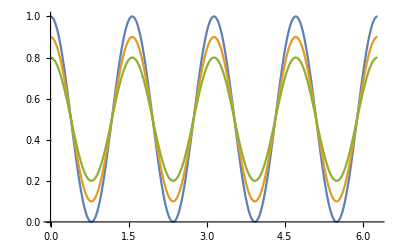

```mathematica
Plot[{probability[1,0,θH,0,0, 0,1,0],probability[1,0,θH,0,0, 0,0.9,0],probability[1,0,θH,0,0, 0,0.8,0]},{θH,0,2π}]
```

```mathematica
Refine[probability[1,0,0,θQ,1,0]//FullSimplify,{α,δ,θH,θQ,β,ϕ}∈Reals && 0<α<1 && 0<β<1&& 0<θH<2π && 0<θQ<2π && 0<δ<2π && 0<ϕ<2π]//FullSimplify
Refine[probability[1,0,0,θQ,0,0]//FullSimplify,{α,δ,θH,θQ,β,ϕ}∈Reals && 0<α<1 && 0<β<1&& 0<θH<2π && 0<θQ<2π && 0<δ<2π && 0<ϕ<2π]//FullSimplify
```

1/4 (3+Cos[4 θQ])

2 Cos[θQ]^2 Sin[θQ]^2

Example shows that the QW doesn’t perform an identical transformation every π/2 rotation:

```mathematica
Refine[(WP[φ,π/2].WP[θ,π])†.Z.(WP[φ,π/2].WP[θ,π])//FullSimplify,{φ,θ}∈Reals]//FullSimplify//MatrixForm
```

(Cos[4 θ-2 φ] Cos[2 φ] | 1/2 (Sin[4 θ]+Sin[4 (θ-φ)]+2 ⅈ Sin[2 φ])
1/2 (Sin[4 θ]+Sin[4 (θ-φ)]-2 ⅈ Sin[2 φ]) | -Cos[4 θ-2 φ] Cos[2 φ])

```mathematica
Refine[(WP[φ+π/2,π/2].WP[θ,π])†.Z.(WP[φ+π/2,π/2].WP[θ,π])//FullSimplify,{φ,θ}∈Reals]//FullSimplify//MatrixForm
```

(Cos[4 θ-2 φ] Cos[2 φ] | 1/2 (Sin[4 θ]+Sin[4 (θ-φ)]-2 ⅈ Sin[2 φ])
1/2 (Sin[4 θ]+Sin[4 (θ-φ)]+2 ⅈ Sin[2 φ]) | -Cos[4 θ-2 φ] Cos[2 φ])

The only way to expose the different transformations is with φ (last term in the off-diagonal components).

```mathematica
(WP[-π/8+π/2,π/2].WP[0,π])†.Z.(WP[-π/8+π/2,π/2].WP[0,π])//FullSimplify//MatrixForm
```

(1/2 | 1/2+ⅈ/(√2)
1/2-ⅈ/(√2) | -1/2)

```mathematica
φ=0;
θ=π/8;
(WP[φ,π/2].WP[θ,π])†.X.(WP[φ,π/2].WP[θ,π])//FullSimplify//MatrixForm
```

(0 | 1
1 | 0)

To test input states preparations:

```mathematica
φ=π/4;
θ=-π/8;
(WP[φ,π/2].WP[θ,π]).(InitialState[1,0]).(InitialState[1,0]†).(WP[φ,π/2].WP[θ,π])†//FullSimplify//MatrixForm
(InitialState[0.5,π/2]).(InitialState[0.5,π/2]†)//MatrixForm
```

(1/2 | -1/2
-1/2 | 1/2)

(0.5+0. ⅈ | 0.-0.5 ⅈ
0.+0.5 ⅈ | 0.5+0. ⅈ)

To test measurement basis: